```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neutron/eth/ki/bin/trained_intnets

# Interaction Networks Permutation Invariance at Training AUC Experiments

## Quantised Networks

## Permutation Invariant Network - with summation layer

```mathematica
gluonAUCs = {0.833,0.833, 0.834, 0.836, 0.834} ;
quarkAUCs = {0.875,0.875, 0.874, 0.876, 0.876};
wAUCs = {0.900,0.899, 0.901, 0.902, 0.894};
zAUCs ={0.882,0.883, 0.883, 0.885, 0.880};
topAUCs ={0.921,0.921, 0.920, 0.921, 0.921};

μpinvGluonAUC = Mean[gluonAUCs];
σpinvGluonAUC = StandardDeviation[gluonAUCs];
μpinvQuarkAUC = Mean[quarkAUCs];
σpinvQuarkAUC = StandardDeviation[quarkAUCs];
μpinvWAUC = Mean[wAUCs];
σpinvWAUC = StandardDeviation[wAUCs];
μpinvZAUC = Mean[zAUCs];
σpinvZAUC = StandardDeviation[zAUCs];
μpinvTopAUC = Mean[topAUCs];
σpinvTopAUC = StandardDeviation[topAUCs];
```

## Permutation Variant Network - without summation layer

```mathematica
gluonAUCs = {0.836,0.838, 0.836, 0.836, 0.836} ;
quarkAUCs = {0.876,0.877, 0.876, 0.876, 0.877};
wAUCs = {0.903,0.896, 0.896, 0.895, 0.898};
zAUCs ={0.885,0.884, 0.883, 0.883, 0.885};
topAUCs ={0.923,0.923, 0.924, 0.923, 0.923};

μpvarGluonAUC = Mean[gluonAUCs];
σpvarGluonAUC = StandardDeviation[gluonAUCs];
μpvarQuarkAUC = Mean[quarkAUCs];
σpvarQuarkAUC = StandardDeviation[quarkAUCs];
μpvarWAUC = Mean[wAUCs];
σpvarWAUC = StandardDeviation[wAUCs];
μpvarZAUC = Mean[zAUCs];
σpvarZAUC = StandardDeviation[zAUCs];
μpvarTopAUC = Mean[topAUCs];
σpvarTopAUC = StandardDeviation[topAUCs];
```

## Plot Variant vs Invariant AUCs

{{{1,0.834±0.00122474}},{{2,0.8752±0.00083666}},{{3,0.8992±0.00311448}},{{4,0.8826±0.00181659}},{{5,0.9208±0.000447214}}}

{{{1,0.8364±0.000894427}},{{2,0.8764±0.000547723}},{{3,0.8976±0.00320936}},{{4,0.884±0.001}},{{5,0.9232±0.000447214}}}

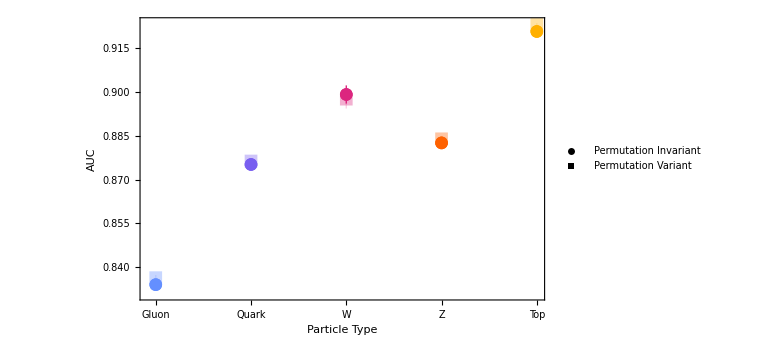

```mathematica
invariantPoints = {μpinvGluonAUC,μpinvQuarkAUC,μpinvWAUC,μpinvZAUC,μpinvTopAUC};
invariantErrors = {σpinvGluonAUC,σpinvQuarkAUC,σpinvWAUC,σpinvZAUC,σpinvTopAUC};

variantPoints ={μpvarGluonAUC,μpvarQuarkAUC,μpvarWAUC,μpvarZAUC,μpvarTopAUC};
variantErrors ={σpvarGluonAUC,σpvarQuarkAUC,σpvarWAUC,σpvarZAUC,σpvarTopAUC};

particleTypes = {1,2,3,4,5};
invariantData =Table[invariantPoints[[i]]±invariantErrors[[i]], {i,1,Length@invariantPoints}];
variantData = Table[variantPoints[[i]]±variantErrors[[i]], {i,1,Length@variantPoints}] ;

invariantPlotData = {#}&/@Transpose[{particleTypes, invariantData}]
variantPlotData = {#}&/@Transpose[{particleTypes, variantData}]

hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.2]}&/@hexColors;

invariantPlot = ListPlot[invariantPlotData, ImageSize->Large, PlotMarkers->{"•", 13}, PlotStyle->hexColors];
variantPlot = ListPlot[variantPlotData,ImageSize->Large, PlotMarkers->{"■", 13}, PlotStyle->lighterHexColors];
plot = Show[variantPlot,invariantPlot, Frame->True, FrameStyle->Directive[15], FrameLabel->{"Particle Type","AUC"}, ImagePadding->65, FrameTicks->{{Automatic, Automatic}, {{{1, "Gluon"},{2, "Quark"}, {3, "W"}, {4,"Z"}, {5,"Top"}},Automatic}}];
legendPlot = Legended[plot,Placed[PointLegend[{Black, Black}, {"Permutation Invariant", "Permutation Variant"}, LegendMarkers->{{"•",15}, {"■",15}}, LabelStyle->13],{0.8,0.15}]]
```

```mathematica
Export["AUC_invariance_qconv_8const.pdf",legendPlot]
```

AUC_invariance_qconv_8const.pdf

## Plot Variant vs Invariant ROCs

```mathematica
baselineTPR=BinaryReadList["perm_invariant_1/plots_seed318/tpr_Gluon.dat","Real32"];
```

```mathematica
permInvQuarkFPR1=BinaryReadList["perm_invariant_1/plots_seed318/fpr_Quark.dat","Real32"];
permInvGluonFPR1=BinaryReadList["perm_invariant_1/plots_seed318/fpr_Gluon.dat","Real32"];
permInvTopFPR1=BinaryReadList["perm_invariant_1/plots_seed318/fpr_Top.dat","Real32"];
permInvWFPR1=BinaryReadList["perm_invariant_1/plots_seed318/fpr_W.dat","Real32"];
permInvZFPR1=BinaryReadList["perm_invariant_1/plots_seed318/fpr_Z.dat","Real32"];

permInvQuarkFPR2=BinaryReadList["perm_invariant_1/plots_seed121/fpr_Quark.dat","Real32"];
permInvGluonFPR2=BinaryReadList["perm_invariant_1/plots_seed121/fpr_Gluon.dat","Real32"];
permInvTopFPR2=BinaryReadList["perm_invariant_1/plots_seed121/fpr_Top.dat","Real32"];
permInvWFPR2=BinaryReadList["perm_invariant_1/plots_seed121/fpr_W.dat","Real32"];
permInvZFPR2=BinaryReadList["perm_invariant_1/plots_seed121/fpr_Z.dat","Real32"];

permInvQuarkFPR3=BinaryReadList["perm_invariant_1/plots_seed591/fpr_Quark.dat","Real32"];
permInvGluonFPR3=BinaryReadList["perm_invariant_1/plots_seed591/fpr_Gluon.dat","Real32"];
permInvTopFPR3=BinaryReadList["perm_invariant_1/plots_seed591/fpr_Top.dat","Real32"];
permInvWFPR3=BinaryReadList["perm_invariant_1/plots_seed591/fpr_W.dat","Real32"];
permInvZFPR3=BinaryReadList["perm_invariant_1/plots_seed591/fpr_Z.dat","Real32"];

permInvQuarkFPR4=BinaryReadList["perm_invariant_1/plots_seed909/fpr_Quark.dat","Real32"];
permInvGluonFPR4=BinaryReadList["perm_invariant_1/plots_seed909/fpr_Gluon.dat","Real32"];
permInvTopFPR4=BinaryReadList["perm_invariant_1/plots_seed909/fpr_Top.dat","Real32"];
permInvWFPR4=BinaryReadList["perm_invariant_1/plots_seed909/fpr_W.dat","Real32"];
permInvZFPR4=BinaryReadList["perm_invariant_1/plots_seed909/fpr_Z.dat","Real32"];

permInvQuarkFPR5=BinaryReadList["perm_invariant_1/plots_seed777/fpr_Quark.dat","Real32"];
permInvGluonFPR5=BinaryReadList["perm_invariant_1/plots_seed777/fpr_Gluon.dat","Real32"];
permInvTopFPR5=BinaryReadList["perm_invariant_1/plots_seed777/fpr_Top.dat","Real32"];
permInvWFPR5=BinaryReadList["perm_invariant_1/plots_seed777/fpr_W.dat","Real32"];
permInvZFPR5=BinaryReadList["perm_invariant_1/plots_seed777/fpr_Z.dat","Real32"];
```

```mathematica
permInvQuarkFPR={permInvQuarkFPR1, permInvQuarkFPR2, permInvQuarkFPR3, permInvQuarkFPR4, permInvQuarkFPR5};
μpermInvQuarkFPR=Mean[permInvQuarkFPR];
σpermInvQuarkFPR=StandardDeviation[permInvQuarkFPR];

permInvGluonFPR={permInvGluonFPR1,permInvGluonFPR2,permInvGluonFPR3,permInvGluonFPR4,permInvGluonFPR5};
μpermInvGluonFPR=Mean[permInvGluonFPR];
σpermInvGluonFPR=StandardDeviation[permInvGluonFPR];

permInvTopFPR={permInvTopFPR1,permInvTopFPR2,permInvTopFPR3,permInvTopFPR4,permInvTopFPR5};
μpermInvTopFPR=Mean[permInvTopFPR];
σpermInvTopFPR=StandardDeviation[permInvTopFPR];

permInvWFPR={permInvWFPR1,permInvWFPR2,permInvWFPR3,permInvWFPR4,permInvWFPR5};
μpermInvWFPR=Mean[permInvWFPR];
σpermInvWFPR=StandardDeviation[permInvWFPR];

permInvZFPR={permInvZFPR1,permInvZFPR2,permInvZFPR3,permInvZFPR4,permInvZFPR5};
μpermInvZFPR=Mean[permInvZFPR];
σpermInvZFPR=StandardDeviation[permInvZFPR];
```

```mathematica
permVarQuarkFPR1=BinaryReadList["perm_variant_1/plots_seed318/fpr_Quark.dat","Real32"];
permVarGluonFPR1=BinaryReadList["perm_variant_1/plots_seed318/fpr_Gluon.dat","Real32"];
permVarTopFPR1=BinaryReadList["perm_variant_1/plots_seed318/fpr_Top.dat","Real32"];
permVarWFPR1=BinaryReadList["perm_variant_1/plots_seed318/fpr_W.dat","Real32"];
permVarZFPR1=BinaryReadList["perm_variant_1/plots_seed318/fpr_Z.dat","Real32"];

permVarQuarkFPR2=BinaryReadList["perm_variant_1/plots_seed121/fpr_Quark.dat","Real32"];
permVarGluonFPR2=BinaryReadList["perm_variant_1/plots_seed121/fpr_Gluon.dat","Real32"];
permVarTopFPR2=BinaryReadList["perm_variant_1/plots_seed121/fpr_Top.dat","Real32"];
permVarWFPR2=BinaryReadList["perm_variant_1/plots_seed121/fpr_W.dat","Real32"];
permVarZFPR2=BinaryReadList["perm_variant_1/plots_seed121/fpr_Z.dat","Real32"];

permVarQuarkFPR3=BinaryReadList["perm_variant_1/plots_seed591/fpr_Quark.dat","Real32"];
permVarGluonFPR3=BinaryReadList["perm_variant_1/plots_seed591/fpr_Gluon.dat","Real32"];
permVarTopFPR3=BinaryReadList["perm_variant_1/plots_seed591/fpr_Top.dat","Real32"];
permVarWFPR3=BinaryReadList["perm_variant_1/plots_seed591/fpr_W.dat","Real32"];
permVarZFPR3=BinaryReadList["perm_variant_1/plots_seed591/fpr_Z.dat","Real32"];

permVarQuarkFPR4=BinaryReadList["perm_variant_1/plots_seed909/fpr_Quark.dat","Real32"];
permVarGluonFPR4=BinaryReadList["perm_variant_1/plots_seed909/fpr_Gluon.dat","Real32"];
permVarTopFPR4=BinaryReadList["perm_variant_1/plots_seed909/fpr_Top.dat","Real32"];
permVarWFPR4=BinaryReadList["perm_variant_1/plots_seed909/fpr_W.dat","Real32"];
permVarZFPR4=BinaryReadList["perm_variant_1/plots_seed909/fpr_Z.dat","Real32"];

permVarQuarkFPR5=BinaryReadList["perm_variant_1/plots_seed777/fpr_Quark.dat","Real32"];
permVarGluonFPR5=BinaryReadList["perm_variant_1/plots_seed777/fpr_Gluon.dat","Real32"];
permVarTopFPR5=BinaryReadList["perm_variant_1/plots_seed777/fpr_Top.dat","Real32"];
permVarWFPR5=BinaryReadList["perm_variant_1/plots_seed777/fpr_W.dat","Real32"];
permVarZFPR5=BinaryReadList["perm_variant_1/plots_seed777/fpr_Z.dat","Real32"];
```

```mathematica
permVarQuarkFPR={permVarQuarkFPR1,permVarQuarkFPR2,permVarQuarkFPR3,permVarQuarkFPR4,permVarQuarkFPR5};
μpermVarQuarkFPR=Mean[permVarQuarkFPR];
σpermVarQuarkFPR=StandardDeviation[permVarQuarkFPR];

permVarGluonFPR={permVarGluonFPR1,permVarGluonFPR2,permVarGluonFPR3,permVarGluonFPR4,permVarGluonFPR5};
μpermVarGluonFPR=Mean[permVarGluonFPR];
σpermVarGluonFPR=StandardDeviation[permVarGluonFPR];

permVarTopFPR={permVarTopFPR1,permVarTopFPR2,permVarTopFPR3,permVarTopFPR4,permVarTopFPR5};
μpermVarTopFPR=Mean[permVarTopFPR];
σpermVarTopFPR=StandardDeviation[permVarTopFPR];

permVarWFPR={permVarWFPR1,permVarWFPR2,permVarWFPR3,permVarWFPR4,permVarWFPR5};
μpermVarWFPR=Mean[permVarWFPR];
σpermVarWFPR=StandardDeviation[permVarWFPR];

permVarZFPR={permVarZFPR1,permVarZFPR2,permVarZFPR3,permVarZFPR4,permVarZFPR5};
μpermVarZFPR=Mean[permVarZFPR];
σpermVarZFPR=StandardDeviation[permVarZFPR];
```

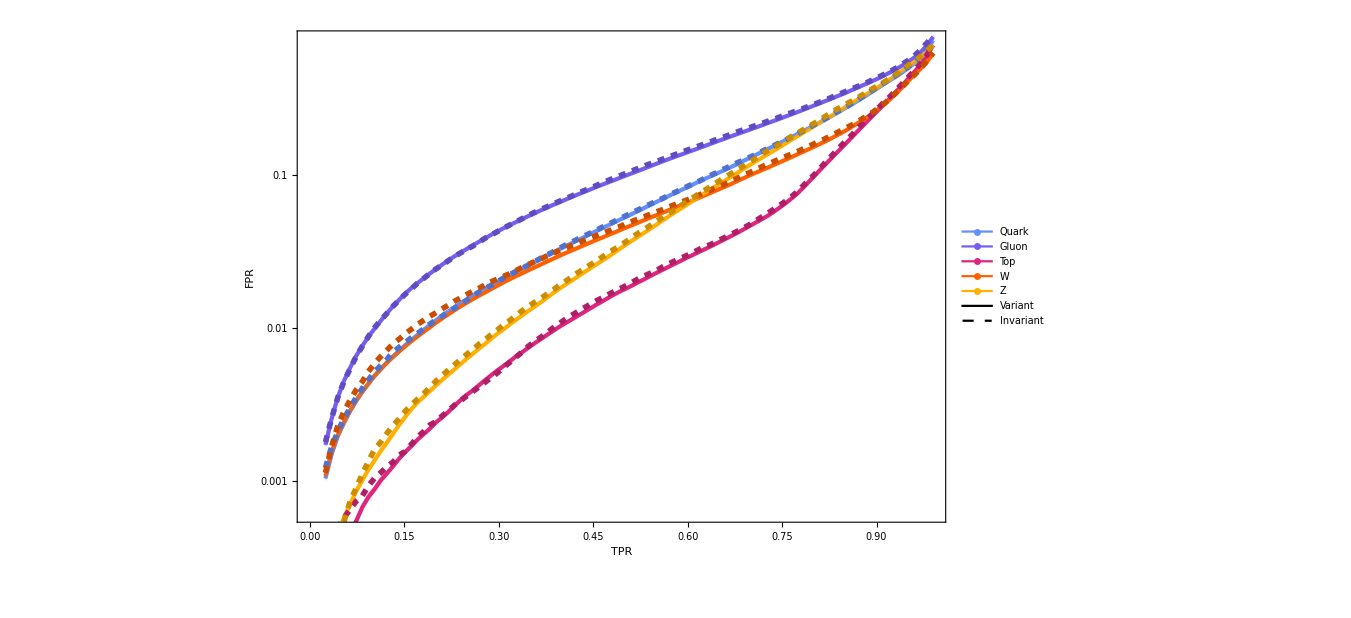

```mathematica
μinvariantFPRs = {μpermInvQuarkFPR, μpermInvGluonFPR, μpermInvTopFPR, μpermInvWFPR, μpermInvZFPR};
σinvariantFPRs = {σpermInvQuarkFPR, σpermInvGluonFPR, σpermInvTopFPR, σpermInvWFPR, σpermInvZFPR};

invariantFPRs=μinvariantFPRs;
invariantFPRsTop=Table[μinvariantFPRs[[i]][[j]]+σinvariantFPRs[[i]][[j]], {i,1,Length@μinvariantFPRs},{j,1, Length@μinvariantFPRs[[i]]}];
invariantFPRsBot=Table[μinvariantFPRs[[i]][[j]]-σinvariantFPRs[[i]][[j]], {i,1,Length@μinvariantFPRs},{j,1, Length@μinvariantFPRs[[i]]}];

invariantCurves = Table[Transpose[{baselineTPR, invariantFPRs[[i]]}],{i, 1, Length@invariantFPRs}];
invariantCurvesTop = Table[Transpose[{baselineTPR, invariantFPRsTop[[i]]}],{i, 1, Length@invariantFPRs}];
invariantCurvesBot = Table[Transpose[{baselineTPR, invariantFPRsBot[[i]]}],{i, 1, Length@invariantFPRs}];

μvariantFPRs={μpermVarQuarkFPR,μpermVarGluonFPR,μpermVarTopFPR,μpermVarWFPR,μpermVarZFPR};
σvariantFPRs={σpermVarQuarkFPR,σpermVarGluonFPR,σpermVarTopFPR,σpermVarWFPR,σpermVarZFPR};

variantFPRs=μvariantFPRs;
variantFPRsTop=Table[μvariantFPRs[[i]][[j]]+σvariantFPRs[[i]][[j]],{i,1,Length@μvariantFPRs},{j,1,Length@μvariantFPRs[[i]]}];
variantFPRsBot=Table[μvariantFPRs[[i]][[j]]-σvariantFPRs[[i]][[j]],{i,1,Length@μvariantFPRs},{j,1,Length@μvariantFPRs[[i]]}];

variantCurves=Table[Transpose[{baselineTPR,variantFPRs[[i]]}],{i,1,Length@variantFPRs}];
variantCurvesTop=Table[Transpose[{baselineTPR,variantFPRsTop[[i]]}],{i,1,Length@variantFPRs}];
variantCurvesBot=Table[Transpose[{baselineTPR,variantFPRsBot[[i]]}],{i,1,Length@variantFPRs}];

hexColors = {"#648FFF","#785EF0","#DC267F","#FE6100","#FFB000"};
hexColors = Map[RGBColor, hexColors];
lighterHexColors = {#, Opacity[0.2]}&/@hexColors;
darkerHexColors = {Darker[#,0.2]}&/@hexColors;

plot=Show[Table[ListLogPlot[variantCurves[[i]], PlotStyle->{hexColors[[i]], Thickness[0.003]},Joined->True],{i,1,Length@variantCurves}],
Table[ListLogPlot[{variantCurvesTop[[i]],variantCurvesBot[[i]]},
PlotStyle->{lighterHexColors[[i]], lighterHexColors[[i]]},Joined->True, Filling->{1->{2}}, FillingStyle->lighterHexColors[[i]]],{i,1,Length@variantCurvesTop}], 
Table[ListLogPlot[invariantCurves[[i]],Joined->True, PlotStyle->Directive[darkerHexColors[[i]],Thickness[0.004], Dashed]],{i,1,Length@invariantCurves}],
ImageSize->1000, Frame->True, FrameStyle->Directive[20], FrameLabel->{"TPR","FPR"}, ImagePadding->110, ImageResolution->300];

legendPlot = Legended[plot,Placed[LineLegend[{hexColors[[1]], hexColors[[2]], hexColors[[3]], hexColors[[4]], hexColors[[5]]}, {"Quark", "Gluon",  "Top", "W", "Z"}, LegendMarkers->Graphics[{Thickness[.3], Line[{{0,0},{10,0}}]}],LabelStyle->{18, Bold}],{0.9,0.2}]];
legendPlot = Legended[legendPlot,Placed[LineLegend[{Black, {Black, Dashed}}, {"Variant", "Invariant"},LabelStyle->{18, Bold}],{0.73,0.11}]]
```

```mathematica
Export["ROC_invariance_qconv_8const.pdf",legendPlot]
```

ROC_invariance_qconv_8const.pdf